## Linear Stability Analysis with Matter

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/linear-stability

```mathematica
Get["../../neupackage/mma/linearstability.wl"]
```

```mathematica
{{
(lambda0+lambda1 Sin[km z1]-alpha mu-eta omegav)/Sin[thetaL],(alpha mu)/Sin[thetaL]
},{
-mu/Sin[thetaR],(lambda0+lambda1 Sin[km z1]+mu+eta omegav)/Sin[thetaR]
}}.{{
(lambda0+lambda1 Sin[km z2]-alpha mu-eta omegav)/Sin[thetaL],(alpha mu)/Sin[thetaL]
},{
-mu/Sin[thetaR],(lambda0+lambda1 Sin[km z2]+mu+eta omegav)/Sin[thetaR]
}}
-
{{
(lambda0+lambda1 Sin[km z2]-alpha mu-eta omegav)/Sin[thetaL],(alpha mu)/Sin[thetaL]
},{
-mu/Sin[thetaR],(lambda0+lambda1 Sin[km z2]+mu+eta omegav)/Sin[thetaR]
}}.{{
(lambda0+lambda1 Sin[km z1]-alpha mu-eta omegav)/Sin[thetaL],(alpha mu)/Sin[thetaL]
},{
-mu/Sin[thetaR],(lambda0+lambda1 Sin[km z1]+mu+eta omegav)/Sin[thetaR]
}}//FullSimplify//MatrixForm
```

{{-alpha mu^2 Csc[thetaL] Csc[thetaR]+Csc[thetaL]^2 (lambda0-alpha mu-eta omegav+lambda1 Sin[km z1]) (lambda0-alpha mu-eta omegav+lambda1 Sin[km z2]),alpha mu Csc[thetaL]^2 (lambda0-alpha mu-eta omegav+lambda1 Sin[km z1])+alpha mu Csc[thetaL] Csc[thetaR] (lambda0+mu+eta omegav+lambda1 Sin[km z2])},{-mu Csc[thetaR]^2 (lambda0+mu+eta omegav+lambda1 Sin[km z1])-mu Csc[thetaL] Csc[thetaR] (lambda0-alpha mu-eta omegav+lambda1 Sin[km z2]),-alpha mu^2 Csc[thetaL] Csc[thetaR]+Csc[thetaR]^2 (lambda0+mu+eta omegav+lambda1 Sin[km z1]) (lambda0+mu+eta omegav+lambda1 Sin[km z2])}}

(Csc[thetaL] (alpha mu^2 Csc[thetaR]-Csc[thetaL] (lambda0-alpha mu-eta omegav+lambda1 Sin[km z1]) (lambda0-alpha mu-eta omegav+lambda1 Sin[km z2])) | alpha mu Csc[thetaL] (-Csc[thetaR] (lambda0+mu+eta omegav+lambda1 Sin[km z1])+Csc[thetaL] (-lambda0+alpha mu+eta omegav-lambda1 Sin[km z2]))
mu Csc[thetaR] (Csc[thetaL] (lambda0-alpha mu-eta omegav+lambda1 Sin[km z1])+Csc[thetaR] (lambda0+mu+eta omegav+lambda1 Sin[km z2])) | Csc[thetaR] (alpha mu^2 Csc[thetaL]-Csc[thetaR] (lambda0+mu+eta omegav+lambda1 Sin[km z1]) (lambda0+mu+eta omegav+lambda1 Sin[km z2])))

Linear Stability Analysis Constant Matter

```mathematica
Eigenvalues[
{{
lambda0+lambda1 Sin[km z]-alpha mu/2-eta omegav,alpha mu /2
},{
-mu/2,lambda0+lambda1 Sin[km z]+mu /2+eta omegav
}}
]//FullSimplify
```

{lambda0-1/4 (-1+alpha) mu-1/4 √((-1+alpha)^2 mu^2+8 (1+alpha) eta mu omegav+16 eta^2 omegav^2)+lambda1 Sin[km z],1/4 (4 lambda0+mu-alpha mu+√((-1+alpha)^2 mu^2+8 (1+alpha) eta mu omegav+16 eta^2 omegav^2)+4 lambda1 Sin[km z])}

```mathematica
Solve[(-1+alpha)^2 mu^2+8 (1+alpha) eta mu omegav+16 eta^2 omegav^2==0,mu]//FullSimplify
```

{{mu→-(4 eta omegav)/(-1+√alpha)^2},{mu→-(4 eta omegav)/(1+√alpha)^2}}

```mathematica
√((-1+alpha)^2 mu^2+8 (1+alpha) eta mu omegav+16 eta^2 omegav^2)
```

2 Beams Fast Mode

```mathematica
theory2Kappa[eta_,mu_,alpha_,thetaL_,thetaR_,lambda0_]:=Module[{omegaM,alphaM,muM,etaM},
etaM=eta;
omegaM=-(-lambda0)/2(1/Sin[thetaL]-1/Sin[Pi-thetaR]);
muM=2mu(1-Cos[thetaL-thetaR])/Sin[thetaR];
alphaM=alpha Sin[Pi-thetaR]/Sin[thetaL];

{"Upper Limit "<>ToString[
Abs[muM/omegaM]<4/(1-√alphaM)^2
],"Lower Limit "<>ToString[
4/(1+√alphaM)^2<Abs[muM/omegaM]
],
N@omegaM√((1-alphaM)^2muM^2/omegaM^2-8etaM(1+alphaM)muM/omegaM)/4}

]
```

```mathematica
sol2Beams[eta_,mu_,alpha_,thetaL_,thetaR_,lambda0_,lambda1_,km_,z_,{zrangestart_,zrangeend_},omegav_:0]:=Module[{delVecM,delMatM,delLM,delRM,sysM,initM,zM,solM},

delVecM[zM_]={delLM[zM],delRM[zM]};
delMatM[zM_]={{
(lambda0+lambda1 Sin[km z]-alpha mu (1-Cos[thetaL-thetaR])-eta omegav)/Sin[thetaL],(alpha mu (1-Cos[thetaL-thetaR]))/Sin[thetaL]
},{
-mu(1-Cos[thetaL-thetaR])/Sin[thetaR],(lambda0+lambda1 Sin[km z]+mu (1-Cos[thetaL-thetaR])+eta omegav)/Sin[thetaR]
}};
initM=delVecM[0]=={10^{-6},10^{-6}};

sysM=I D[delVecM[z],z]==(delMatM[z].delVecM[z]);

solM=NDSolve[sysM&&initM,{delLM,delRM},{z,zrangestart,zrangeend}];

{Table[{zM,Log@First@Abs[delLM[zM]/.First@solM]},{zM,zrangestart,zrangeend,1}],
Table[{zM,Log@First@Abs[delRM[zM]/.First@solM]},{zM,zrangestart,zrangeend,1}]
}
]
```

```mathematica
pltdatalist=sol2Beams[-1,1,0.9,Pi/6,Pi-Pi/3,0.7,0,10,z,{0,100}];
```

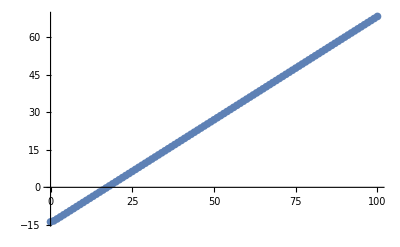

```mathematica
ListPlot[pltdatalist[[1]]]
```

```mathematica
FindFit[pltdatalist[[1]],a x+b,{a,b},x]
```

{a→0.825811,b→-14.2797}

```mathematica
theory2Kappa[-1,1,0.9,Pi/6,Pi-Pi/3,0.7]
```

{Upper Limit True,Lower Limit True,0.989073}

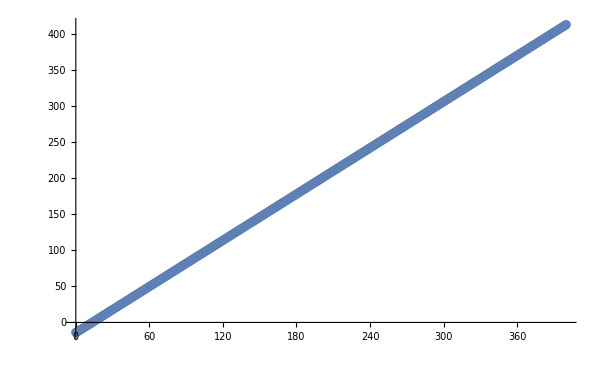
{-Graphics-,Slope: 1.06791,{Upper Limit True,Lower Limit True,1.27947},1.1981}

```mathematica
Module[{etaM,muM,alphaM,thetaLM,thetaRM,lambda0M,lambda1M,kmM,omegavM,pltdatalistM},

etaM=-1;
muM=1.3;
alphaM=0.9;
thetaLM=Pi/6;
thetaRM=Pi-Pi/3;
lambda0M=0.9;
lambda1M=0;
kmM=10;



pltdatalistM=sol2Beams[etaM,muM,alphaM,thetaLM,thetaRM,lambda0M,lambda1M,kmM,z,{0,400}];

{
ListPlot[pltdatalistM[[1]],ImageSize->600],
"Slope: "<>ToString[
a/.FindFit[pltdatalistM[[1]],a x+b,{a,b},x]
],
theory2Kappa[etaM,muM,alphaM,thetaLM,thetaRM,lambda0M],
theory2Kappa[etaM,muM,alphaM,thetaLM,thetaRM,lambda0M][[3]]/(a/.FindFit[pltdatalistM[[1]],a x+b,{a,b},x])
}

]
```

Non Fast Modes

```mathematica
theoryKappa2BeamsNF[eta_,mu_,alpha_,lambda0_]:=Module[{omegaM,alphaM,muM,etaM,thetaRM},

etaM=eta;
omegaM=1;
muM=mu;
alphaM=alpha ;

{"Upper Limit "<>ToString[
Abs[muM/omegaM]<4/(1-√alphaM)^2
],"Lower Limit "<>ToString[
4/(1+√alphaM)^2<Abs[muM/omegaM]
],
N@omegaM√((1-alphaM)^2muM^2/omegaM^2-8etaM(1+alphaM)muM/omegaM)/4,
N@Im@√(-(1-alphaM)^2muM^2+8etaM(1+alphaM)muM/omegaM)/4}


]
```

```mathematica
sol2BeamsNF[eta_,mu_,alpha_,lambda0_,lambda1_,km_,z_,{zrangestart_,zrangeend_},omegav_:1]:=Module[{delVecM,delMatM,delLM,delRM,sysM,initM,zM,solM,thetaRM},


delVecM[zM_]={delLM[zM],delRM[zM]};
delMatM[zM_]={{
lambda0+lambda1 Sin[km z]-alpha mu/2-eta omegav,alpha mu /2
},{
-mu/2,lambda0+lambda1 Sin[km z]+mu /2+eta omegav
}};

initM=delVecM[0]=={10^{-6},10^{-6}};

sysM=I D[delVecM[z],z]==(delMatM[z].delVecM[z]);

solM=NDSolve[sysM&&initM,{delLM,delRM},{z,zrangestart,zrangeend}];

{
Table[{zM,Log@First@Abs[delLM[zM]/.First@solM]},{zM,zrangestart,zrangeend,1}],
Table[{zM,Log@First@Abs[delRM[zM]/.First@solM]},{zM,zrangestart,zrangeend,1}]
}


]
```

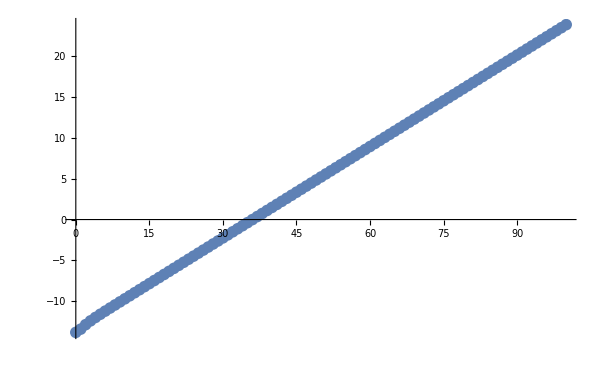
{-Graphics-,Slope: 0.37358,{Upper Limit True,Lower Limit True,1.06813,1.06813},2.85917}

```mathematica
Module[{etaM,muM,alphaM,lambda0M,lambda1M,kmM,omegavM,pltdatalistM},

etaM=-1;
muM=1.2;
alphaM=0.9;
lambda0M=0.9;
lambda1M=0;
kmM=10;



pltdatalistM=sol2BeamsNF[etaM,muM,alphaM,lambda0M,lambda1M,kmM,z,{0,100}];

{
ListPlot[pltdatalistM[[2]],ImageSize->600],
"Slope: "<>ToString[
a/.FindFit[pltdatalistM[[2]],a x+b,{a,b},x]
],
theoryKappa2BeamsNF[etaM,muM,alphaM,lambda0M],
theoryKappa2BeamsNF[etaM,muM,alphaM,lambda0M][[3]]/(a/.FindFit[pltdatalistM[[2]],a x+b,{a,b},x])
}

]
```

Four Beams

```mathematica
kappaSpecificValues[alpha_,mk_,theta1_,theta2_,lambda0_,mu_]:=Module[{etaM,alphaM,lambdaM,muS,muE,mkS,mkE,densityM,mkListM,muListM,muStepM,mkStepM,theta1M,theta2M,pltM,dataM,transMatrixM},

etaM=-1;
alphaM=alpha;
lambdaM=lambda0;
muS=0;
muE=100;
mkS=0;
mkE=50;
muStepM=1;
mkStepM=1;
theta1M=theta1;
theta2M=theta2;



(*dataM=Table[{mu,
Max[
Im@Eigenvalues[
FourBeamTransMatrix[etaM,mk,mu,alphaM,theta1M,theta2M,lambdaM,1]
]
]
},
{mu,muS,muE,muStepM}];


pltM=ListPlot[dataM,PlotLegends->Automatic,PlotLabel->"Maximum value of imaginary part of eigenvalues\n"<>"α="<>ToString[alphaM]<>"; {θ_1,θ_2}="<>ToString[TraditionalForm@{theta1M,theta2M}],ImageSize->600,FrameLabel->{"μ","κ"},Frame->True];

pltM

*)

{mu,
Max[
Im@Eigenvalues[
FourBeamTransMatrix[etaM,mk,mu,alphaM,theta1M,theta2M,lambdaM,1]
]
]}

]
```

```mathematica
sol4Beams[eta_,mk_,mu_,alpha_,thetaL_,thetaR_,lambda0_,lambda1_,km_,z_,{zrangestart_,zrangeend_},omegav_:0]:=Module[{delVecM,delMatM,delLM,delRM,sysM,initM,zM,solM,mM},

mM=mk;

delVecM[zM_]={deltaL[zM],deltaLB[zM],deltaR[zM],deltaRB[zM]};
delMatM[zM_]=FourBeamTransMatrix[eta,mM,mu,alpha,thetaL,thetaR,lambda0 +lambda1 Cos[km zM],omegav];
initM=delVecM[0]=={10^{-5},10^{-5},10^{-5},10^{-5}};

sysM=I D[delVecM[z],z]==(delMatM[z].delVecM[z]);

solM=NDSolve[sysM&&initM,{deltaL,deltaLB,deltaR,deltaRB},{z,zrangestart,zrangeend},MaxSteps->1000000];


{
Table[{zM,Log[Exp[1],First@Abs[deltaL[zM]/.First@solM]]},{zM,zrangestart,zrangeend,1}],
Table[{zM,Log@First@Abs[deltaLB[zM]/.First@solM]},{zM,zrangestart,zrangeend,1}],
Table[{zM,Log@First@Abs[deltaR[zM]/.First@solM]},{zM,zrangestart,zrangeend,1}],
Table[{zM,Log@First@Abs[deltaRB[zM]/.First@solM]},{zM,zrangestart,zrangeend,1}]
}


]
```

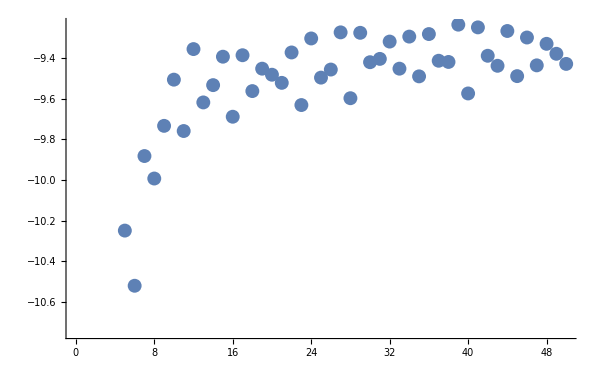
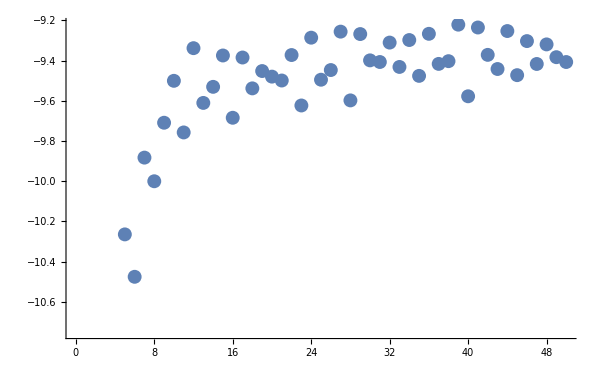
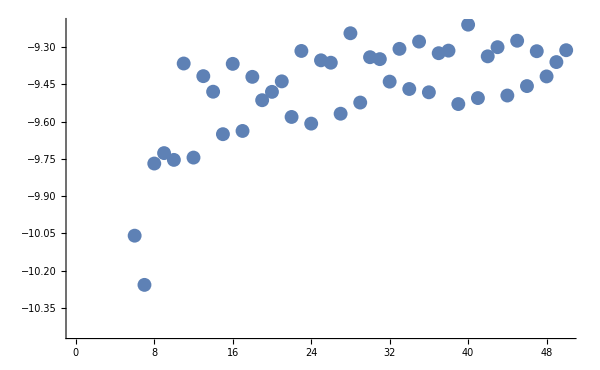
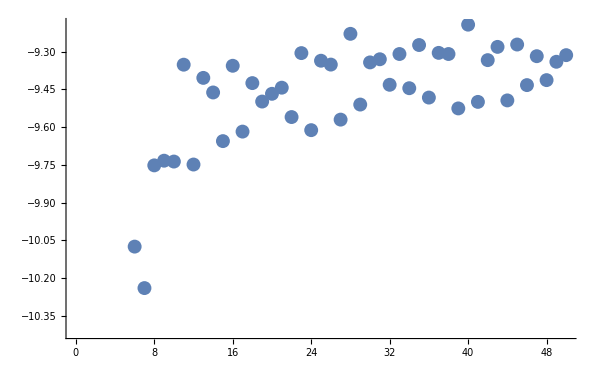
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Slope: 0.00305705 | Slope: 0.00312799 | Slope: 0.00390093 | Slope: 0.00384687
For only background matter profile: {μ,κ}={800, 0} |  |  |

```mathematica
Module[{etaM,muM,alphaM,lambda0M,lambda1M,kmM,omegavM,pltdatalistM,theta1M,theta2M,mkM},

etaM=1;
muM=800;
alphaM=0.8;
lambda0M=0;
lambda1M=100;
theta1M=Pi/6;
theta2M=Pi/6;
mkM=0;
kmM=800;(*matter profile*)

pltdatalistM=sol4Beams[etaM,mkM,muM,alphaM,theta1M,theta2M,lambda0M,lambda1M,kmM,z,{0,50},1];

{
Table[
ListPlot[pltdatalistM[[i]],ImageSize->600],
{i,1,4}],
Table["Slope: "<>ToString[
a/.FindFit[pltdatalistM[[i]][[20;;]],a x+b,{a,b},x]
],
{i,1,4}],
{"For only background matter profile: {μ,κ}="<>ToString@kappaSpecificValues[alphaM,mkM,theta1M,theta2M,lambda0M,muM]}

}//Grid

]
```

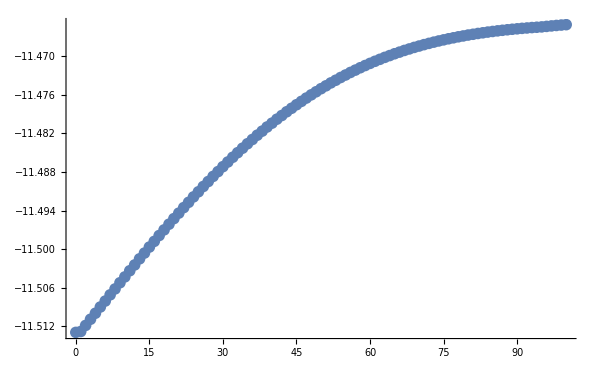
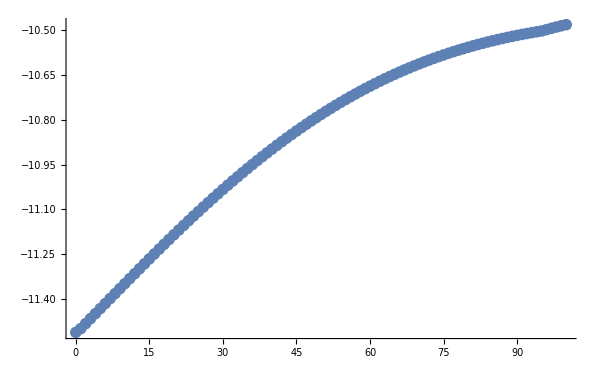
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Slope: 0.000365147 | Slope: 0.00873918 | Slope: 0.000365147 | Slope: 0.00873918
For only background matter profile: {μ,κ}={0, 0} |  |  |

```mathematica
Module[{etaM,muM,alphaM,lambda0M,lambda1M,kmM,omegavM,pltdatalistM,theta1M,theta2M,mkM,omegamM,thetaVacM},

thetaVacM=0;

etaM=1;
muM=0;
alphaM=0.8;
lambda0M=0;
lambda1M=5;
theta1M=Pi/6;
theta2M=Pi/6;
mkM=0;
omegavM =1;
omegamM= √((lambda0M-omegavM Cos[2thetaVacM])^2+omegavM^2 Sin[thetaVacM]^2);
kmM=0.008omegamM;(*matter profile*)


pltdatalistM=sol4Beams[etaM,mkM,muM,alphaM,theta1M,theta2M,lambda0M,lambda1M,kmM,z,{0,100},omegavM];

{
Table[
ListPlot[pltdatalistM[[i]],ImageSize->600],
{i,1,4}],
Table["Slope: "<>ToString[
a/.FindFit[pltdatalistM[[i]][[20;;]],a x+b,{a,b},x]
],
{i,1,4}],
{"For only background matter profile: {μ,κ}="<>ToString@kappaSpecificValues[alphaM,mkM,theta1M,theta2M,lambda0M,muM]}

}//Grid

]
```

## Phase Plane

```mathematica
decoupledModes[etaM_,mu_,alphaM_,theta1M_,theta2M_,lambdaM_,omegav_]:=FourBeamRotationMatrixDiffAngle.FourBeamTransMatrix[etaM,0,mu,alphaM,theta1M,theta2M,lambdaM,omegav].Inverse@FourBeamRotationMatrixDiffAngle
```

```mathematica
decoupledModes[eta,mu,alpha,theta1,theta2,lambda,omegav][[3;;4,3;;4]]//FullSimplify//MatrixForm
```

((lambda+2 mu-2 alpha mu-eta omegav+2 mu Cos[2 theta1]) Csc[theta1]+2 alpha mu Sin[theta2] | -2 alpha mu Cos[theta2] Cot[theta1]
2 mu Cos[theta1] Cot[theta2] | (lambda+(2-4 alpha) mu+eta omegav) Csc[theta2]-2 mu Sin[theta1]+4 alpha mu Sin[theta2])

```mathematica
decoupledModes[eta,mu,alpha,theta1,theta2,lambda,omegav][[3;;4,3;;4]]//FullSimplify//MatrixForm
```

((lambda+2 mu-2 alpha mu-eta omegav+2 mu Cos[2 theta1]) Csc[theta1]+2 alpha mu Sin[theta2] | -2 alpha mu Cos[theta2] Cot[theta1]
2 mu Cos[theta1] Cot[theta2] | (lambda+(2-4 alpha) mu+eta omegav) Csc[theta2]-2 mu Sin[theta1]+4 alpha mu Sin[theta2])

```mathematica
nullLines[etaM_,mu_,alphaM_,theta1M_,theta2M_,lambdaM_,omegav_,x_,y_]:=decoupledModes[eta,mu,alpha,theta1,theta2,lambda,omegav][[3;;4,3;;4]].{x,y}//FullSimplify
```

```mathematica
nullLines[eta,mu,alpha,theta1,theta2,lambda,omegav,1,1]
```

```mathematica
muFun1[eta_,alpha_,theta1_,theta2_,lambda_,omegav_]:=(lambda-eta omegav)/(2 (-1+alpha-Cos[2 theta1]+alpha Cos[theta1+theta2]))(*mu/.First@Solve[nullLines[eta,mu,alpha,theta1,theta2,lambda,omegav,1,1][[1]]==0,mu]*)
muFun2[eta_,alpha_,theta1_,theta2_,lambda_,omegav_]:=(lambda+eta omegav)/(2 (-1+alpha+alpha Cos[2 theta2]-Cos[theta1+theta2]))(*mu/.First@Solve[nullLines[eta,mu,alpha,theta1,theta2,lambda,omegav,1,1][[2]]==0,mu]*)
```

```mathematica
Module[{theta1M,theta2M,etaM,lambdaM,omegavM,dataM,pltM},
theta1M=Pi/6;
theta2M=Pi/3;
lambdaM=0;
omegavM=1;
etaM=1;


dataM={
Table[
{alpha,muFun1[etaM,alpha,theta1M,theta2M,lambdaM,omegavM]},
{alpha,0,2,0.1}],
Table[
{alpha,muFun2[etaM,alpha,theta1M,theta2M,lambdaM,omegavM]},
{alpha,0,2,0.1}]
};

pltM=ListPlot[{
Table[
{alpha,muFun1[etaM,alpha,theta1M,theta2M,lambdaM,omegavM]},
{alpha,0,2,0.1}],
Table[
{alpha,muFun2[etaM,alpha,theta1M,theta2M,lambdaM,omegavM]},
{alpha,0,2,0.1}]
}
];

dataM



]
```

{{{0.,0.333333},{0.1,0.357143},{0.2,0.384615},{0.3,0.416667},{0.4,0.454545},{0.5,0.5},{0.6,0.555556},{0.7,0.625},{0.8,0.714286},{0.9,0.833333},{1.,1.},{1.1,1.25},{1.2,1.66667},{1.3,2.5},{1.4,5.},{1.5,ComplexInfinity},{1.6,-5.},{1.7,-2.5},{1.8,-1.66667},{1.9,-1.25},{2.,-1.}},{{0.,-0.5},{0.1,-0.526316},{0.2,-0.555556},{0.3,-0.588235},{0.4,-0.625},{0.5,-0.666667},{0.6,-0.714286},{0.7,-0.769231},{0.8,-0.833333},{0.9,-0.909091},{1.,-1.},{1.1,-1.11111},{1.2,-1.25},{1.3,-1.42857},{1.4,-1.66667},{1.5,-2.},{1.6,-2.5},{1.7,-3.33333},{1.8,-5.},{1.9,-10.},{2.,ComplexInfinity}}}